{9,11,8,11,7,8,11,7,4,7,11,9,7,7,7,11,11,7,7,9,8,7,9,9,11,8,5,7,5,10,7,9,9,7,5,6,7,10,7,8,9,6,5,5,8,10,8,11,6,11,11,7,7,9,7,10,4,8,7,4,7,9,7,7,6,9,7,8,7,8,8,7,6,7,7,6,6,7,11,7,7,5,7,6,7,7,8,5,7,7,4,7,6,6,6,5,7,7,7,6,7,7,6,6,10,11,7,7,7,4,11,4,11,9,4,11,7,7,9,7,7,5,8,8,11,8,8,6,4,11,6,8,9,11,5,8,7,7,6,5,7,4,9,11,7,6,8,6,6,11,8,7,7,5,11,6,7,7,11,6,11,4,7,8,6,6,6,7,4,10,7,5,7,11,7,7,6,9,8,7,11,9,11,7,11,7,8,5,7,7,7,7,7,8,11,7,7,7,11,11,6,5,7,10,10,8,7,6,11,4,7,11,7,7,6,10,11,11,6,9,11,11,10,6,11,7,4,9,10,7,11,4,7,8,7,9,9,11,7,7,9,7,5,10,11,6,5,7,8,7,7,11,6,10,7,6,7,11,5,7,7,7,9,9,8,5,7,11,5,6,7,11,5,6,11,6,11,7,5,7,6,7,4,6,8,11,11,7,9,7,7,8,8,4,11,7,8,7,4,7,6,7,7,7,6,7,6,7,7,6,11,5,7,10,11,7,7,11,8,11,9,7,11,7,7,8,8,8,6,8,7,7,10,8,10,6,10,7,5,7,8,8,6,6,5,7,5,9,7,7,11,7,8,11,5,8,10,7,7,5,5,5,7,7,4,6,9,7,8,11,8,8,6,11,10,7,7,6,7,10,5,9,7,4,11,9,7,8,6,11,8,8,7,9,10,6,7,6,6,7,7,7,9,7,7,11,7,7,9,7,7,8,9,9,6,9,8,6,7,7,7,6,9,9,7,8,11,7,7,6,6,11,9,8,6,7,11,9,7,7,5,8,9,7,5,10,5,11,7,7,10,9,10,6,6,6,7,7,7,7,8,7,8,6,11,7,9,7,7,7,9,7,7,6,11,4,9,7,7,6,6,11,11,11,6,7,11,6,9,11,9,6,8,11,6,10,7,8,7,6,6}

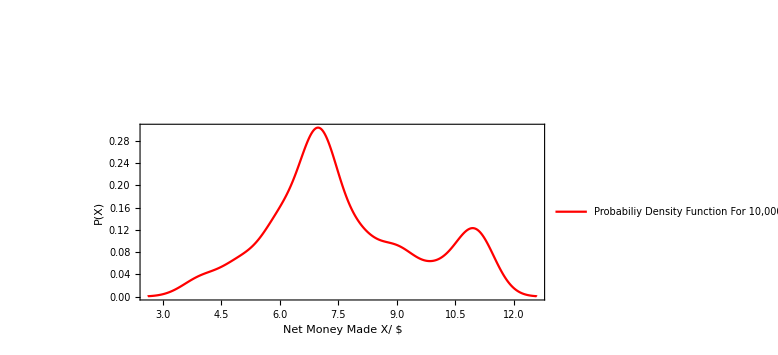

```mathematica
firstDie = 0;
secondDie = 0;
rollSum = 0;
myPoint = 0;
numberOfWins = 0; 
numberOfReplications = 1000; 
numberOfGames = 1000; 
inneriterator = 0;
winChoice = 1; 
outerIterator = 0; 
fairWinningProbability = List[]; 
ProbabilityOfWinning = 0;
While [outerIterator < numberOfGames,

While [inneriterator < numberOfReplications,
	firstDie = RandomInteger[5]+1;
	secondDie = RandomInteger[5]+1;
	rollSum = firstDie + secondDie;

	If [rollSum == 7 ∨ rollSum == 11,
		winChoice = 1; 
		numberOfWins++
	];
	If [ rollSum ==2 ∨ rollSum == 3 ∨ rollSum == 12,
		winChoice = 0;
          ];
	If [rollSum ≠ 7 ∧rollSum ≠ 11 ∧rollSum ≠ 2 ∧rollSum ≠ 3 ∧rollSum ≠ 12,		
			myPoint = rollSum; 
			firstDie = RandomInteger[5]+1;
			secondDie = RandomInteger[5]+1;
			rollSum = firstDie + secondDie; 
			While [rollSum ≠ myPoint ∧ rollSum ≠ 7,
					firstDie = RandomInteger[5]+1;
					secondDie = RandomInteger[5]+1;
					rollSum = firstDie + secondDie; 
				];
			If[myPoint == rollSum,
				winChoice = 1; 
				numberOfWins++,
				winChoice = 0; 
			];
				
	];

inneriterator++;
];
ProbabilityOfWinning = ProbabilityOfWinning + numberOfWins/numberOfReplications;
If [winChoice == 1, 
AppendTo[fairWinningProbability, rollSum]; 
];
inneriterator = 0; 
numberOfWins = 0; 
outerIterator++;
];
fairWinningProbability
dataHistogram = SmoothHistogram[fairWinningProbability, GridLines-> { {Mean[fairWinningProbability]}}, GridLinesStyle-> Dashed,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made X/ $","P(X)","Conditions= 
Starting Money = $40000; 
Money gained per each correct throw = $50;
FAIR dye i.e. P(WIN) = 3/6, P(LOSS) = 3/6
",""}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+Mean[fairWinningProbability] //N}},Alignment->{{Left}}],Background->White],{11.5,0.80},{Right,Top}] ,  PlotLegends->{"Probabiliy Density Function For 10,000 Trials"},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
```

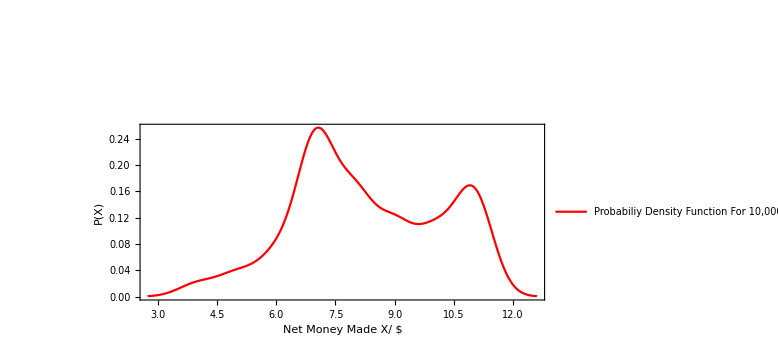
```mathematica
firstDie = 0;
secondDie = 0;
rollSum = 0;
myPoint = 0;
numberOfWins = 0; 
numberOfReplications = 100; 
numberOfGames = 1000; 
inneriterator = 0;
winChoice = 1; 
outerIterator = 0; 
fairWinningProbability = List[]; 
ProbabilityOfWinning = 0;
unfairDyeList = List[1,2,2,3,3,4,4,5,5,6,6,6,6];

While [outerIterator < numberOfGames,

While [inneriterator < numberOfReplications,
	firstDie = unfairDyeList[[RandomInteger[12]+1]];
	secondDie = unfairDyeList[[RandomInteger[12]+1]];
	rollSum = firstDie + secondDie;

	If [rollSum == 7 ∨ rollSum == 11,
		winChoice = 1; 
		numberOfWins++
	];
	If [ rollSum ==2 ∨ rollSum == 3 ∨ rollSum == 12,
		winChoice = 0;
          ];
	If [rollSum ≠ 7 ∧rollSum ≠ 11 ∧rollSum ≠ 2 ∧rollSum ≠ 3 ∧rollSum ≠ 12,		
			myPoint = rollSum; 
			firstDie = unfairDyeList[[RandomInteger[12]+1]];
			secondDie = unfairDyeList[[RandomInteger[12]+1]];
			rollSum = firstDie + secondDie; 
			While [rollSum ≠ myPoint ∧ rollSum ≠ 7,
					firstDie = unfairDyeList[[RandomInteger[12]+1]];
					secondDie = unfairDyeList[[RandomInteger[12]+1]];
					rollSum = firstDie + secondDie; 
				];
			If[myPoint == rollSum,
				winChoice = 1; 
				numberOfWins++,
				winChoice = 0; 
			];
				
	];

inneriterator++;
];
ProbabilityOfWinning = ProbabilityOfWinning + numberOfWins/numberOfReplications;
If [winChoice == 1, 
AppendTo[fairWinningProbability, rollSum]; 
];
inneriterator = 0; 
numberOfWins = 0; 
outerIterator++;
];
fairWinningProbability

dataHistogram = SmoothHistogram[fairWinningProbability, GridLines-> { {Mean[fairWinningProbability]}}, GridLinesStyle-> Dashed,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"Net Money Made X/ $","P(X)","Conditions= 
Starting Money = $40000; 
Money gained per each correct throw = $50;
FAIR dye i.e. P(WIN) = 3/6, P(LOSS) = 3/6
",""}, Epilog->Inset[Framed[Grid[{{"Average Money Made($) = "+Mean[fairWinningProbability] //N}},Alignment->{{Left}}],Background->White],{11.5,0.80},{Right,Top}] ,  PlotLegends->{"Probabiliy Density Function For 10,000 Trials"},LabelStyle->{FontSize->14, Directive[Bold,Black]}, PlotStyle->{RGBColor[1,0,0],PointSize[0.005]}]
-Graphics-
```

{5,9,7,11,9,7,10,11,8,10,7,7,5,7,6,5,6,10,9,8,7,6,4,7,11,11,8,11,6,8,11,11,7,10,10,7,9,10,8,11,8,8,11,11,8,6,9,8,8,7,8,9,7,8,9,5,8,9,8,7,11,7,7,9,8,6,6,6,8,7,11,6,8,6,7,6,9,8,7,11,10,7,7,4,8,4,11,7,8,11,8,11,11,11,7,11,9,8,5,4,7,6,8,9,7,8,8,11,10,11,7,8,6,6,7,11,8,8,6,11,10,7,9,7,8,8,10,9,9,7,10,8,8,4,7,8,11,9,5,8,9,11,8,6,7,5,6,10,9,10,8,8,8,11,7,10,8,11,7,11,8,10,9,7,7,7,11,5,6,11,11,8,4,8,9,8,8,9,10,8,7,8,7,7,11,7,11,11,10,11,8,11,11,6,7,4,7,5,7,5,8,11,7,11,7,11,11,7,7,10,6,10,11,4,7,10,7,7,10,5,10,7,5,7,8,11,7,7,11,7,8,8,6,11,10,9,7,11,11,11,11,8,6,7,4,7,7,7,7,9,7,10,9,8,5,7,7,10,7,8,9,8,9,9,11,7,8,7,9,11,9,7,10,8,8,7,7,9,7,10,4,7,8,10,11,4,8,11,11,8,9,10,9,6,7,5,7,8,5,11,7,8,8,9,7,7,7,6,11,8,8,8,8,9,7,6,5,9,7,7,7,11,7,8,8,4,8,7,8,8,8,5,7,11,4,10,9,5,7,7,11,10,10,7,8,8,8,7,7,11,8,8,7,10,6,10,10,8,7,10,6,7,8,8,10,7,11,6,8,11,6,7,7,6,8,8,8,10,8,7,11,4,8,7,8,8,9,6,7,7,7,7,4,10,7,7,7,6,9,8,7,8,7,7,6,10,10,4,6,4,7,10,4,7,7,7,5,7,7,9,8,8,10,4,9,11,6,11,11,7,7,9,7,10,11,5,8,11,8,7,10,6,9,9,9,9,11,7,11,7,11,8,8,9,7,7,7,9,8,8,9,11,7,7,7,11,7,11,11,11,7,11,7,8,7,6,7,7,6,4,10,11,10,6,11,10,7,9,9,11,8,10,11,10,10,9,7,8,5,9,7,9,10,7,8,7,6,9,11,10,4,11,11,7,10,7,10,8,10,11,11,10,7}

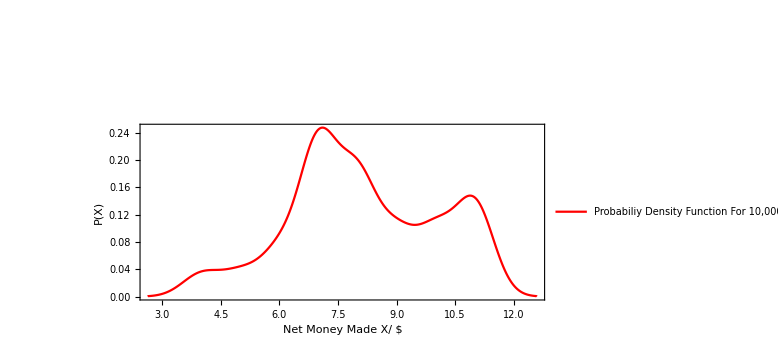

-Graphics-